# helper

```mathematica
getBlack[s_]:=StringCases[s,("B<< Monte-Carlo "~~Shortest[__]~~" total games: "~~(x:DigitCharacter..)~~WordBoundary):>ToExpression[x]/10^6];
getWhite[s_]:=StringCases[s,("W<< Monte-Carlo "~~Shortest[__]~~" total games: "~~(x:DigitCharacter..)~~WordBoundary):>ToExpression[x]/10^6]
```

```mathematica
ClearAll[makePlot];
makePlot[expr_->data_]:=
Module[{all},
all=Join[getBlack[data],getWhite[data]];
all=all;ListLinePlot[{Legended[Style[Take[all,Length[getBlack[data]]],Black],Placed["Black",Below]],Legended[Style[Drop[all,Length[getBlack[data]]],LightGray],Placed["White",Below]]},PlotLabel->StringTrim[expr,"\\"]];
ListLinePlot[{getWhite[data],getBlack[data]},Mesh->All,PlotLabel->Style[StringTrim[expr,"\\"],Medium],PlotRange->All,PlotMarkers->{Automatic,8},PlotStyle->{LightGray,Black}]]
```

```mathematica
?PlotMarkers
```

PlotMarkers is an option for graphics functions like ListPlot and ListLinePlot that specifies what markers to draw at the points plotted.

## MPI

```mathematica
SetDirectory[NotebookDirectory[]];
rawdata=Map[FileNameSplit[#][[2]]->Import[#,"Text"]&,FileNames["*/gtg_output.txt",{"1","2","3"}]];
```

```mathematica
data=Normal@Map[Function[{val},StringJoin[Last/@val]],GroupBy[rawdata,StringJoin[Riffle[Most[StringSplit[First[#],"_"]]," "]]&]];
```

```mathematica
Length[data]
```

2

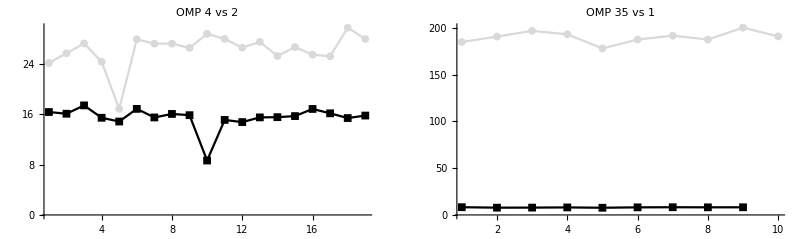

```mathematica
GraphicsRow[makePlot/@Reverse@Sort@Normal[data],ImageSize->Scaled[0.8]]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"adk_19_vs.pdf"}],GraphicsRow[makePlot/@Reverse@Sort@Normal[data],ImageSize->Scaled[2]]]
```

/Users/abduld/cs484/data/adk_19/adk_19_vs.pdf